# Studying SW’s Minimal Model for Biological Evolution

## V1

14

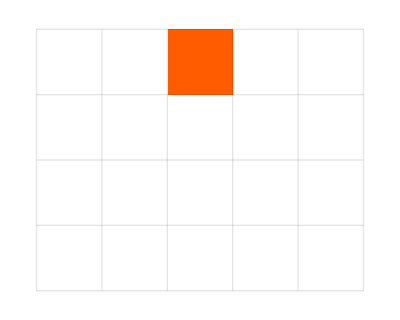
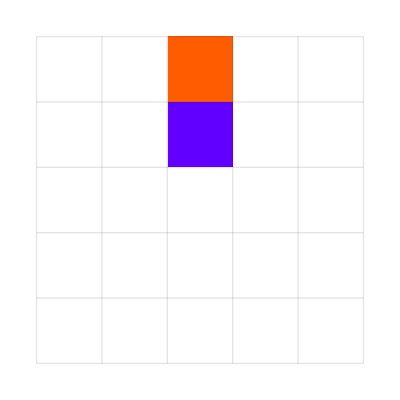
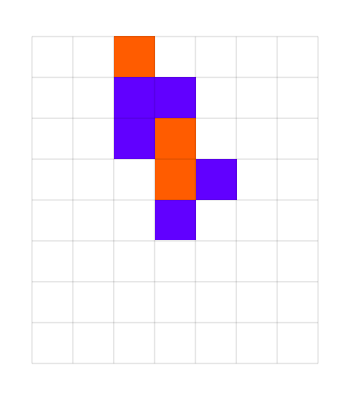
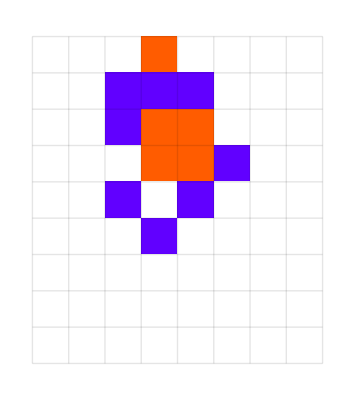
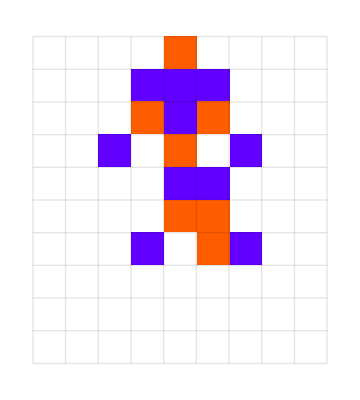
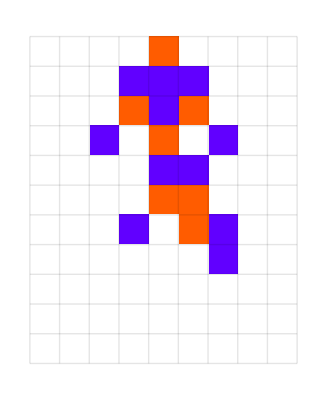
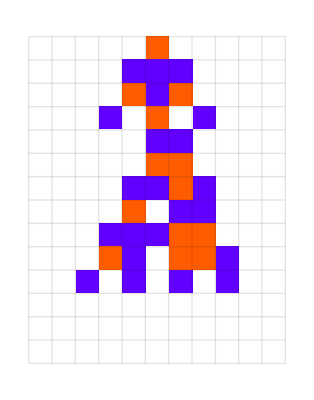
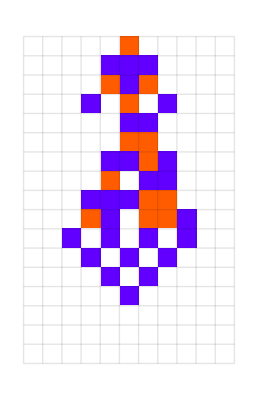

```mathematica
Module[
{deep=5000,cut=200,ru,life,evo,data},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep];
evo=Rest[First/@SplitBy[evo,Last]];
Echo[Length[evo]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
evo]
]
```

```mathematica
RulePlot[]
```

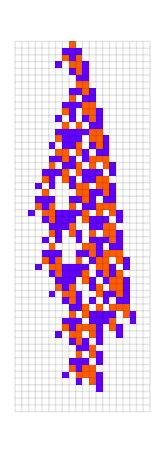

```mathematica
ArrayPlot[CellularAutomaton[{5600111605818,3,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},54],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

```mathematica
plot[rule_, len_:20]:= ArrayPlot[
CellularAutomaton[rule, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, len],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

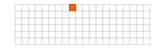

```mathematica
ArrayPlot[
CellularAutomaton[{531441,3,1}, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, 5],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

```mathematica
or = {5600111605818,3,1}
```

{5600111605818,3,1}

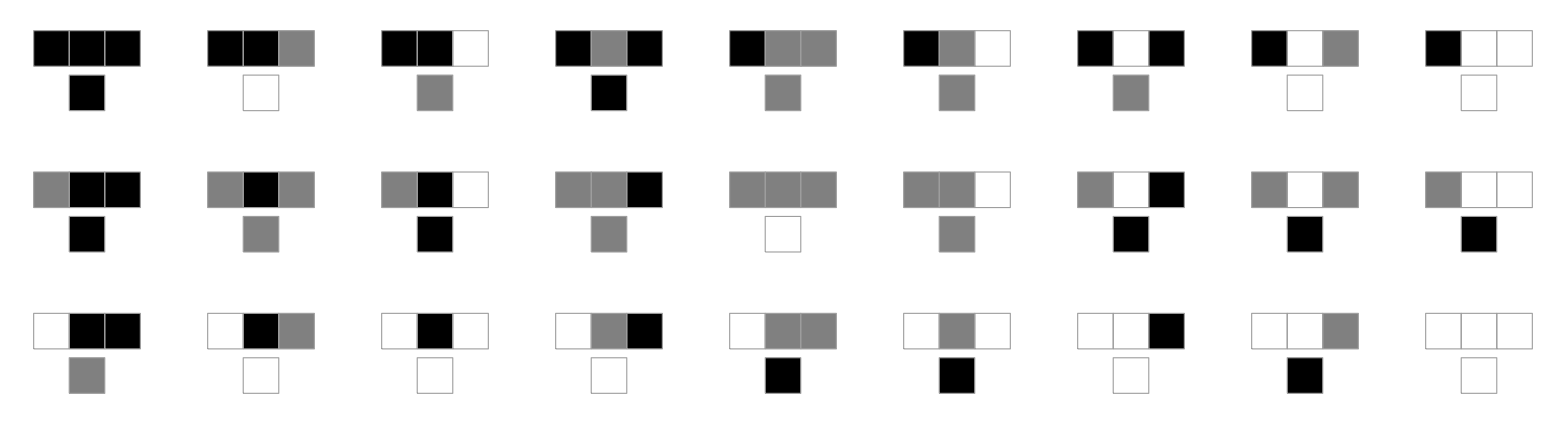

```mathematica
RulePlot[CellularAutomaton[or]]
```

FromDigits::nlst: The expression IntegerDigits[Mod[1+5 ru586032021307,3],3,27] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression IntegerDigits[Mod[2+5 ru586032021307,3],3,27] is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression IntegerDigits[5 ru586032021307,1,27] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

CellularAutomaton::nocol: Since position 2 of rule specification {FromDigits[IntegerDigits[Mod[1+5 ru586032021307,3],3,27],3],3,1} is not {}, position 1 must be an integer or a pure Boolean function.

ArrayPad::arr: First argument CellularAutomaton[{FromDigits[IntegerDigits[Mod[1+5 ru586032021307,3],3,27],3],3,1},{{1},0},30] to ArrayPad should be an array.

CellularAutomaton::nocol: Since position 2 of rule specification {FromDigits[IntegerDigits[Mod[2+5 ru586032021307,3],3,27],3],3,1} is not {}, position 1 must be an integer or a pure Boolean function.

ArrayPad::arr: First argument CellularAutomaton[{FromDigits[IntegerDigits[Mod[2+5 ru586032021307,3],3,27],3],3,1},{{1},0},30] to ArrayPad should be an array.

CellularAutomaton::nocol: Since position 2 of rule specification {FromDigits[IntegerDigits[5 ru586032021307,1,27],3],3,1} is not {}, position 1 must be an integer or a pure Boolean function.

General::stop: Further output of CellularAutomaton::nocol will be suppressed during this calculation.

ArrayPad::arr: First argument CellularAutomaton[{FromDigits[IntegerDigits[5 ru586032021307,1,27],3],3,1},{{1},0},30] to ArrayPad should be an array.

General::stop: Further output of ArrayPad::arr will be suppressed during this calculation.

ArrayPlot::mat: Argument CellularAutomaton[{FromDigits[IntegerDigits[Mod[1+5 ru586032021307,3],3,27],3],3,1},{{1},0},30] at position 1 is not a list of lists.

ArrayPlot::mat: Argument CellularAutomaton[{FromDigits[IntegerDigits[Mod[2+5 ru586032021307,3],3,27],3],3,1},{{1},0},30] at position 1 is not a list of lists.

ArrayPlot::mat: Argument CellularAutomaton[{FromDigits[IntegerDigits[5 ru586032021307,1,27],3],3,1},{{1},0},30] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

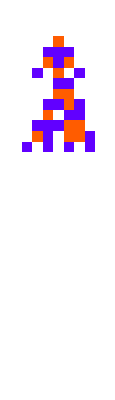
-Graphics- →     ArrayPlot[CellularAutomaton[{FromDigits[IntegerDigits[Mod[1+5 ru586032021307,3],3,27],3],3,1},{{1},0},30],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},FrameStyle→GrayLevel[0.65],ImageSize→{All,70}]ArrayPlot[CellularAutomaton[{FromDigits[IntegerDigits[Mod[2+5 ru586032021307,3],3,27],3],3,1},{{1},0},30],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},FrameStyle→GrayLevel[0.65],ImageSize→{All,70}]ArrayPlot[CellularAutomaton[{FromDigits[IntegerDigits[5 ru586032021307,1,27],3],3,1},{{1},0},30],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},FrameStyle→GrayLevel[0.65],ImageSize→{All,70}]ArrayPlot[CellularAutomaton[{FromDigits[IntegerDigits[5 ru586032021307,2,27],3],3,1},{{1},0},30],ColorRules→{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]},FrameStyle→GrayLevel[0.65],ImageSize→{All,70}]

```mathematica
Module[{ru={5586032021307,3,1},data},
data=Map[ArrayPad[CellularAutomaton[
#,{{1},0},30],{{0,0},{1,1}}]&,
{{"[◼]", "RuleMutationsList"}}[{ru,3,1}]];
PrependTo[data,ArrayPad[CellularAutomaton[
ru,{{1},0},30],{{0,0},{1,1}}]];
data=Map[ArrayPlot[#,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
FrameStyle->GrayLevel[.65],ImageSize->{All,70}
]&,data];
Style[Row[{First[data],Style[" → ",20,Bold,Gray],
Row[Rest[data],"  "]}],LineSpacing->{1.05,.1}]
]
```

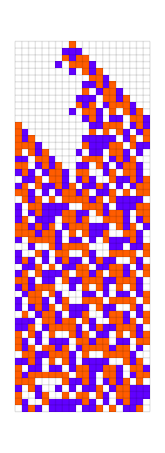

```mathematica
nr = {{"[◼]", "RandomRuleMutation"}}[or];
plot[nr]
```

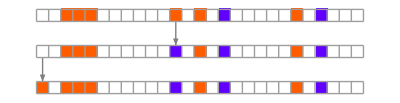

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[426778];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,50}]]]
```

## WN Experimentation

Really my main question is, how does phenotypical space look in the CA model, and how does that compare to phenotypical space in bacteria

So as a first attempt I’m simply going to look at how length can change with point mutations in rules

```mathematica
ru={5586032021307,3,1};
cut = 200;
lt = {{"[◼]", "TestLifetime"}}[ru, cut];
```

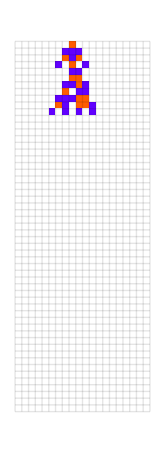

```mathematica
plot[ru]
```

```mathematica
lifetimes = {{"[◼]", "TestLifetime"}}[#, cut]&/@ rulist
```

{-∞,-∞,-∞,-∞,5,4,-∞,-∞,-∞,11,5,10,-∞,14,-∞,-∞,-∞,-∞,11,11,4,4,-∞,-∞,-∞,-∞,11,11,-∞,-∞,5,6,11,11,-∞,-∞,4,4,11,11,-∞,-∞,-∞,-∞,8,-∞,2,-∞,-∞,-∞,-∞,-∞}

What I want is to start from some rule and see which lengths I can jump to. But ofcourse the issue is where you can go depends on where you came from.

```mathematica
NestGraph[]
```

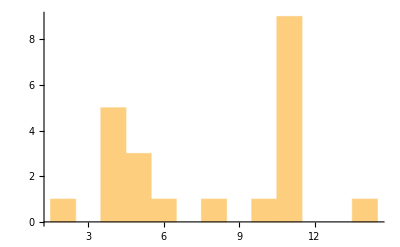

```mathematica
Histogram[lifetimes, 15]
```

```mathematica
edges =
```

```mathematica
Module[{nngraph,lifetimes,subg,res},
nngraph={{"[◼]", "CANearestNeighborGraph"}}[2,1,Range[0,2^(2^3)-1,2],
EdgeStyle->Gray,VertexStyle->Directive[EdgeForm[Opacity[.5]],LightGray]];
lifetimes=Association[Map[#->{{"[◼]", "TestLifetime"}}[
{#,2,1},{1,1,1,0,1,1,1}]&,VertexList[nngraph]]];
subg=Keys[Select[lifetimes,#>=0&]];
res=HighlightGraph[Graph[HighlightGraph[nngraph,Style[
EdgeList[Subgraph[nngraph,subg]],Opacity[.8],Hue[0.68, 0.3, 0.76],Thick]],
EdgeStyle->Directive[Opacity[.3],Gray],
VertexSize->{x_:>If[lifetimes[x]<0,
.5,Sqrt[lifetimes[x]]]},
VertexStyle->{x_:>Directive[
{EdgeForm[{Thickness[.0045],GrayLevel[0,.2]}],
If[lifetimes[x]<0,GrayLevel[.8],
Blend[RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],
(lifetimes[x]-1)/5]]}]}],
Style[0,Green]];
Show[res,
ListPlot[Callout[GraphEmbedding[nngraph][[
FirstPosition[VertexList[nngraph],#][[1]]]],
Labeled[ArrayPlot[CellularAutomaton[#,{{1,1,1,0,1,1,1},0},lifetimes[#]],Mesh->True,MeshStyle->Opacity[.1],ImageSize->21,PlotRangePadding->{{1,1},{0,0}}],
ArrayPlot[{IntegerDigits[#,2,8]},
ImageSize->{Automatic,4}],
Spacings->{0,-1/4}
],
"Appearance"->"Balloon",FrameMargins->None,Background->White
]&/@TakeLargestBy[subg,lifetimes,8],PlotStyle->Opacity[0]]
]
]
```

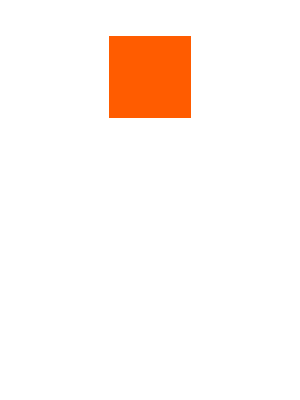
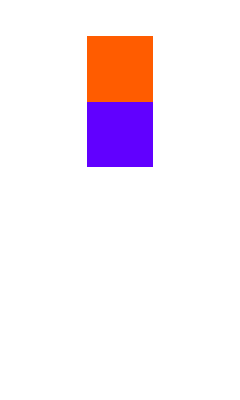
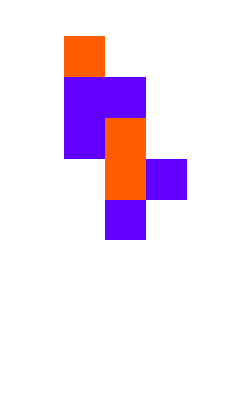
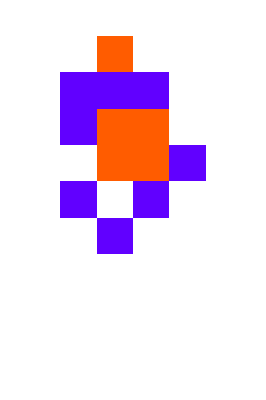
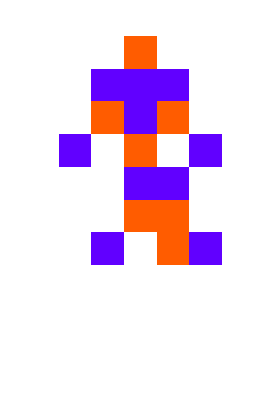
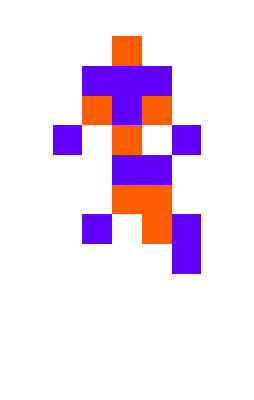
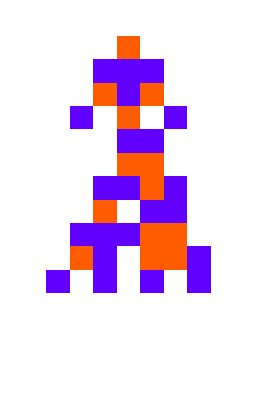
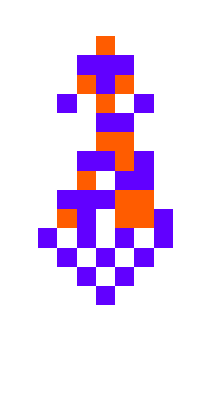
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=5000,cut=200,splits,ru,life,
evo,ball,data,res},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
splits=SplitBy[evo,Last];
evo=First/@splits;
ball=Last/@splits;
ball=MapThread[{{"[◼]", "BallLossPlot"}}[First[#1],
BaselinePosition->Axis,ImageSize->70,"Highlight"->#2[[1]]]&,
{Most[ball],Rest[evo]}];
evo=Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
data=ArrayPad[#,1]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],FrameStyle->GrayLevel[.65],
ImageSize->{Automatic,15Sqrt[Last[#]+2]}
]]&,evo];
Riffle[evo,ball]
]
```

```mathematica
Module[{init,res},
init={{450504084,2,2},308};
res=ResourceFunction["FixedPointGraph"][
{{"[◼]", "IterateMutations"}}[1,Less][#,{1},Last[#]
]&,{init},
GraphLayout->"LayeredDigraphEmbedding",
AspectRatio->1
];
Graph[res,
VertexSize->2/4,
EdgeStyle->Gray,
VertexShapeFunction->Function[
Inset[ArrayPlot[ArrayPad[#,1]&/@
CellularAutomaton[#2[[1]],{{1},0},#2[[2]]+1],
ColorRules->{0->White,1->Black}],#1,Automatic,
{Automatic,Last[#3]Sqrt[ (#2[[2]]+2)]}
]],AspectRatio->.8]
]
```

Graph[Graph[{{{450504084,2,2},308},{{316286356,2,2},22},{{450495892,2,2},27},{{450503060,2,2},9},{{450503828,2,2},2},{{450504080,2,2},2},{{450536852,2,2},25},{{316285332,2,2},9},{{316286100,2,2},2},{{316286352,2,2},2},{{449978772,2,2},5},{{450494868,2,2},6},{{450495636,2,2},2},{{450495888,2,2},2},{{450502804,2,2},2},{{450503056,2,2},2},{{450535828,2,2},9},{{450536596,2,2},2},{{450536848,2,2},2},{{315761044,2,2},5},{{316277140,2,2},6},{{316285076,2,2},2},{{316285328,2,2},2},{{449970580,2,2},5},{{449978516,2,2},2},{{449978768,2,2},2},{{450011540,2,2},5},{{450494612,2,2},2},{{450494864,2,2},2},{{450494900,2,2},5},{{450527636,2,2},6},{{450535572,2,2},2},{{450535824,2,2},2},{{315752852,2,2},5},{{315760788,2,2},2},{{315761040,2,2},2},{{316276884,2,2},2},{{316277136,2,2},2},{{449970324,2,2},2},{{449970576,2,2},2},{{450003348,2,2},5},{{450011284,2,2},2},{{450011536,2,2},2},{{450494644,2,2},2},{{450494884,2,2},4},{{450494896,2,2},2},{{450527380,2,2},2},{{450527632,2,2},2},{{450527668,2,2},5},{{315752596,2,2},2},{{315752848,2,2},2},{{450003092,2,2},2},{{450003344,2,2},2},{{450527412,2,2},2},{{450527652,2,2},4},{{450527664,2,2},2}},{/private/var/folders/_1/8j0kws797tg83z3r45c_770h0000gp/T/m000003301701},GraphLayout→LayeredDigraphEmbedding,AspectRatio→1],VertexSize→1/2,EdgeStyle→GrayLevel[0.5],VertexShapeFunction→(Inset[ArrayPlot[(ArrayPad[#1,1]&)/@CellularAutomaton[#2⟦1⟧,{{1},0},#2⟦2⟧+1],ColorRules→{0→White,1→Black}],#1,Automatic,{Automatic,Last[#3] √(#2⟦2⟧+2)}]&),AspectRatio→0.8]

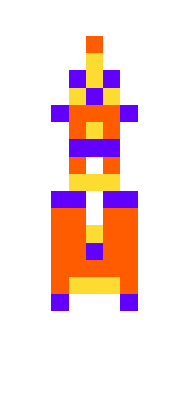
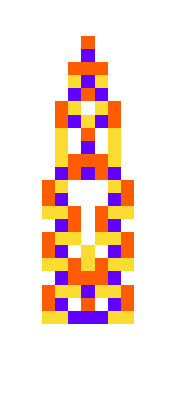
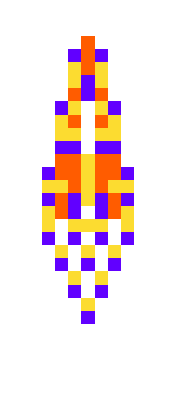
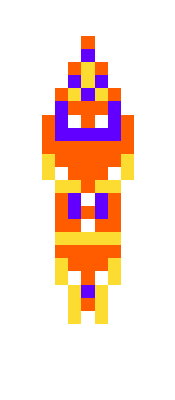
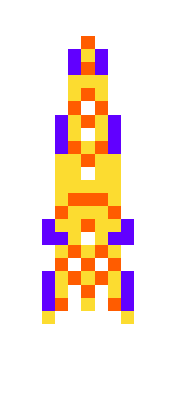
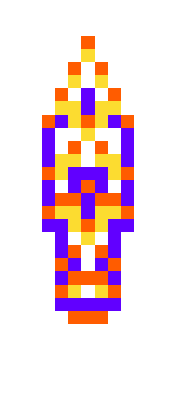
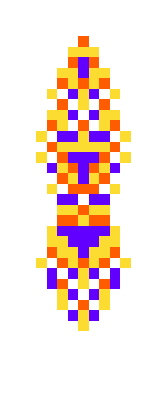
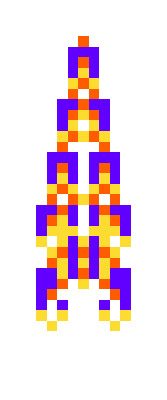
{-Graphics-{16,5}
3.2,-Graphics-{22,7}
3.1429,-Graphics-{22,7}
3.1429,-Graphics-{22,7}
3.1429,-Graphics-{22,7}
3.1429,-Graphics-{22,7}
3.1429,-Graphics-{28,9}
3.1111,-Graphics-{28,9}
3.1111,-Graphics-{47,15}
3.1333,-Graphics-{47,15}
3.1333,-Graphics-{53,17}
3.1176,-Graphics-{60,19}
3.1579,-Graphics-{66,21}
3.1429,-Graphics-{66,21}
3.1429,-Graphics-{85,27}
3.1481,-Graphics-{97,31}
3.129,-Graphics-{110,35}
3.1429,-Graphics-{118,37}
3.1892,-Graphics-{129,41}
3.1463}

```mathematica
Style[With[{data=CellularAutomaton[
#[[1]],{{1},0},#[[2,1]]+2]},
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,20Sqrt[Length[data]+1]}
],Style[Column[{#[[2]],If[IntegerQ[#],#,N[#,5]]&[#[[2,1]]/#[[2,2]]]}],"Text",Italic,Gray,11]]]&/@SortBy[{{{10968520492183531225224276867040509456,4,1},{22,7}},{{30216713568004230552604495370306516232,4,1},{22,7}},{{118816019598574630568259185297076231696,4,1},{22,7}},{{147867524257454613978136825399499213576,4,1},{22,7}},{{247744655389107488374802969842040611648,4,1},{22,7}},{{58815660642501955444073062064274393616,4,1},{66,21}},{{241687037020328885260540818202048692784,4,1},{66,21}},{{17025917258835193437700836692725246236,4,1},{110,35}},{{267227511750712386499495711364875305584,4,1},{129,41}},{{224060214060349828078231208920263117068,4,1},{85,27}},{{299917579853018103739252875933936500232,4,1},{60,19}},{{130381074601791423152459846552751689264,4,1},{118,37}},{{3176185581773832765808516683868972928,4,1},{16,5}},{{131506824482363662793296965881367159880,4,1},{97,31}},{{333492398743405953806947884113537544204,4,1},{47,15}},{{53456945975025449123260531923976946748,4,1},{47,15}},{{241239149133911344725103757603242130188,4,1},{28,9}},{{249901277437000159631971403147031363456,4,1},{53,17}},{{264034764086666528641346401892089692680,4,1},{28,9}}},Last],LineSpacing->{1.1,0}]
```

```mathematica
Graph[Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->GraphicsRow[
ArrayPlot[ArrayPad[#,1]&/@#,ImageSize->{Automatic,(2+key[[1]])10},Mesh->(key[[1]]<5),MeshStyle->Opacity[.1]
]&/@Union[CellularAutomaton[{#,2,2},{{1},0},
key[[1]]+1]&/@rules],Spacings->0,
PlotRangePadding->None
]],sublevels]];
ClearAttributes[vfs,Temporary];
Subgraph[res,VertexOutComponent[res,{0,1}],
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
],VertexCoordinates->]
```

-Graphics-

```mathematica
Module[{lifetimes,res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,2,
GraphLayout->"LayeredDigraphEmbedding"],
{"SubLevels","Lifetimes"}];
sublevels=res[[2,1,1,1]];
lifetimes=res[[2,2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->GraphicsRow[
ArrayPlot[
Rest[CenterArray[#,Dimensions[#]+{2,2}]],ImageSize->{Automatic,(2+key[[1]])10}
]&/@Union[CellularAutomaton[{#,2,2},{{1},0},
key[[1]]+1]&/@rules],Spacings->0,
PlotRangePadding->None
]],sublevels]];
res=Subgraph[res,VertexOutComponent[res,{0,1}],
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/3,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
];
EdgeAdd[res,Reverse/@Select[
EdgeList[res],#[[1]]==#[[2]]-1&]]
]
```

-Graphics-

```mathematica
-Graphics-
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
Module[{nngraph,lifetimes,subg,res},
nngraph={{"[◼]", "CANearestNeighborGraph"}}[2,1,Range[0,2^(2^3)-1,2],
EdgeStyle->Gray,VertexStyle->Directive[EdgeForm[Opacity[.5]],LightGray]];
lifetimes=Association[Map[#->{{"[◼]", "TestLifetime"}}[
{#,2,1},{1,1,1,0,1,1,1}]&,VertexList[nngraph]]];
subg=Keys[Select[lifetimes,#>=0&]];
res=HighlightGraph[Graph[HighlightGraph[nngraph,Style[
EdgeList[Subgraph[nngraph,subg]],Opacity[.8],Hue[0.68, 0.3, 0.76],Thick]],
EdgeStyle->Directive[Opacity[.3],Gray],
VertexSize->{x_:>If[lifetimes[x]<0,
.3,Sqrt[lifetimes[x]]]},
VertexStyle->{x_:>Directive[
{EdgeForm[{Thickness[.0045],GrayLevel[0,.2]}],
If[lifetimes[x]<0,GrayLevel[.8],
Blend[RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],
(lifetimes[x]-1)/5]]}]}],
Style[0,Green]];
lifetimes=ReplaceAll[lifetimes,_DirectedInfinity->-2.5];
Graph3D[res,
ViewVertical->{0,0,1},
EdgeShapeFunction->Function[Line[#1]],
VertexCoordinates->
MapThread[Append,{GraphEmbedding[res],
Lookup[lifetimes,VertexList[res]]/3}]]
]
```

-Graphics3D-

```mathematica
Module[
{goal=50,deep=5000,cut=200,ru,life,evo,data,res},
res=ParallelTable[CompoundExpression[
SeedRandom[745746+i],
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal]<=
Abs[Last[#]-goal],{ru,life},#]
]&,{{0,4,1},0},deep],
evo=Rest[First/@SplitBy[evo,Last]],
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},Last[#]+2],
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,15Sqrt[Length[data]+1]}
],Style[Last[#],"Text",Italic,Gray,11]]
]&,evo]],{i,{2,12,14,21,31,38}}];
Column[Row/@res,Dividers->{
False,Thread[Range[2,5]->LightGray]}]
]
```

$Aborted

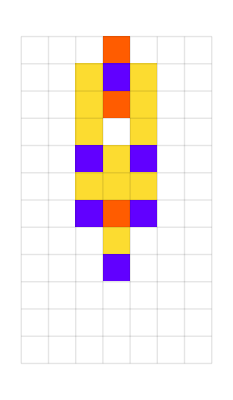
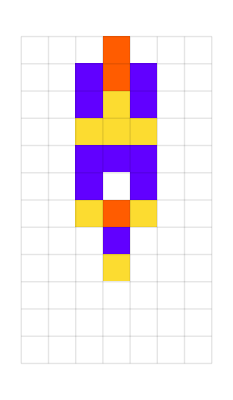
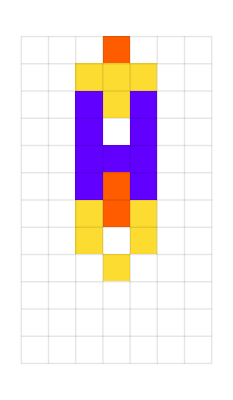
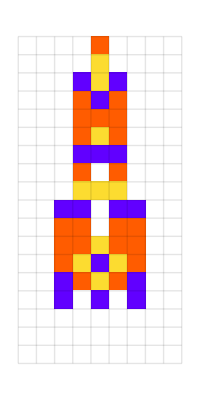
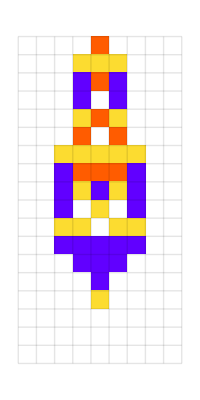
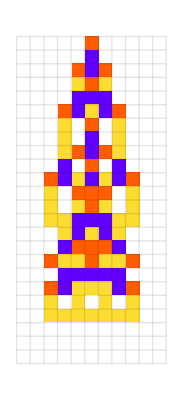
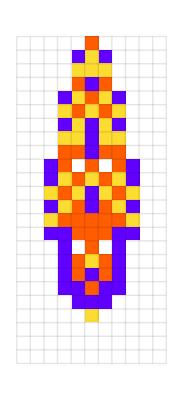
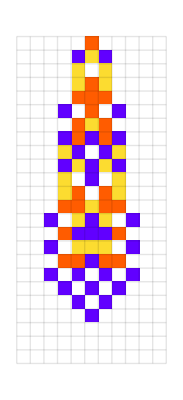
{-Graphics-{9,3},-Graphics-{9,3},-Graphics-{9,3},-Graphics-{15,5},-Graphics-{15,5},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{27,9},-Graphics-{27,9},-Graphics-{39,13},-Graphics-{45,15},-Graphics-{51,17},-Graphics-{57,19},-Graphics-{57,19},-Graphics-{69,23},-Graphics-{69,23},-Graphics-{111,37}}

```mathematica
Style[With[{data=CellularAutomaton[
#[[1]],{{1},0},#[[2,1]]+2]},
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,24Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
],Style[#[[2]],"Text",Italic,Gray,11]]]&/@{{{109636419052937157723438118980837975564,4,1},{9,3}},{{232259557841861635493049224869714791688,4,1},{9,3}},{{338236923684700346441755364009144414988,4,1},{9,3}},{{3663450190864856052378894455912568704,4,1},{15,5}},{{136651796051772457646439217666630305548,4,1},{15,5}},{{74948306682547943335519680440646385168,4,1},{21,7}},{{193464179513193600562914906378802444040,4,1},{21,7}},{{193649253952380488246394671786963518216,4,1},{21,7}},{{298798483958213368517806363132769509688,4,1},{21,7}},{{337623673395850352619393223745807586160,4,1},{21,7}},{{143430394600545658197868087730119774096,4,1},{27,9}},{{246493520306698100424983701858655419148,4,1},{27,9}},{{180664442152675280322045408237394267792,4,1},{39,13}},{{36324902254124465598971313626629143056,4,1},{45,15}},{{289850694849104464885050820643032709680,4,1},{51,17}},{{143923012087109979886256736424975337072,4,1},{57,19}},{{280384207228392989942672757173339297804,4,1},{57,19}},{{283391784414472610606660051001734099568,4,1},{69,23}},{{330335253914559274144004959766636949128,4,1},{69,23}},{{142140648448642989785750794400464692296,4,1},{111,37}}},LineSpacing->{1.1,0}]
```

```mathematica
res = CellularAutomaton[{109636419052937157723438118980837975564,4,1}, {0, 0, 0, 0, 1, 0,0, 0}, 10]
```

{{0,0,0,0,1,0,0,0},{0,0,0,3,2,3,0,0},{0,0,0,3,1,3,0,0},{0,0,0,3,0,3,0,0},{0,0,0,2,3,2,0,0},{0,0,0,3,3,3,0,0},{0,0,0,2,1,2,0,0},{0,0,0,0,3,0,0,0},{0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
rul = {109636419052937157723438118980837975564,4,1};
```

```mathematica
{{"[◼]", "TestLifetime"}}[rul, 100]
```

9

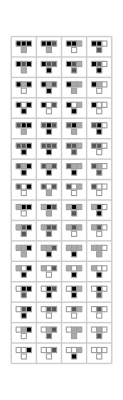

```mathematica
RulePlot[CellularAutomaton[rul]]
```

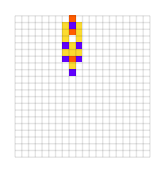

```mathematica
plot[rul]
```

```mathematica
mutes = Table[{{"[◼]", "RandomRuleMutation"}}[rul], 10];
```

```mathematica
selected = Select[mutes, {{"[◼]", "TestLifetime"}}[#, 100]>=9&];
```

```mathematica
Length[selected]
```

8

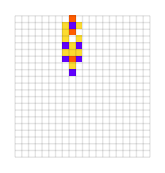
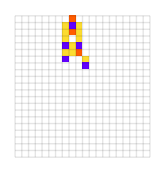
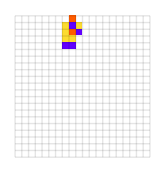
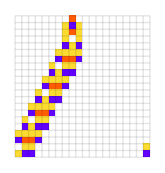
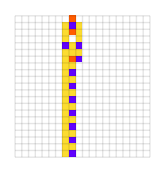
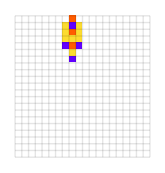
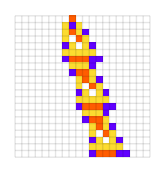
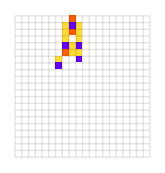
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@ mutes
```

```mathematica
plot[rule_, len_:20]:= ArrayPlot[
CellularAutomaton[rule, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, len],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

## V2 - CAs as the environment

```mathematica
CellularAutomaton[1,{{1},0},100]
```

{{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0},{0,0,0},{0,1,0}}

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},100], Mesh->True]
```

-Graphics-

So my idea here is to have have a set of rules for “jumping” as the genotype. Black is death white is life. You get 10 organisms. You can vary genotype by changing the jump direction by one unit. The meta evolution function is how often you choose to vary your organism. Consider one bit directional jumps.  When one organism dies out you get to proliferate a whole new set of organisms.

A “species” is an array of 1 bit rules. That contains a quantity and a jump distance. This quantity can either be incremented or decremented

Actually let’s just say that you can either jump 1 to the right, one to the left or stay the same. From those options, you can either

So a species is represented as an array, as well as some metadata. Each element in the array is an organism. An organism contains a position (phenotype), and a rule (genotype) for how to update the position. For now we’ll limit the genotype to 3 options: jump to the right, jump to the left, or stay in the middle. The metadata for a species for now is it tells you how it updates the gene pool. So when an organism “dies” the surviving ones fill it in. Specifically, it is populated by the first survivor. Then the last two organisms are mutated by “incrementing” the rule, so if it is +1 then it goes to -1, if it’s -1 it goes to 0.

Actually if it dies you would ideally want it to be taken over by the cell that was nearest to it in phenotype space, because that’s where “the new energy” is in the environment. So we’ll say when an organism dies a new one is created that’s closest to it defaulting to the left one if it finds multiple.

```mathematica
orgs = Table[<|"loc"->0, "rule"->0|>, 10]
```

{<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>}

```mathematica
species = <|"meta"->{"adaptionfunction"}, "organisms"->orgs|>
```

<|meta→{},organisms→{<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>,<|loc→0,rule→0|>}|>

```mathematica
adapt[func_, rule_]:= func[rule]
```

```mathematica
findclosest[loc_,organisms_]:=
  Module[{distances,closestIndex},
    distances=Abs[organisms[[All,"loc"]]-loc];
    closestIndex=First@Ordering[distances];
    organisms[[closestIndex]]
  ]
```

```mathematica
landscape = CellularAutomaton[110,{{1},0},100];
```

Make a function iterate that takes a species as input and

```mathematica
Replace[{0, 0, 0, 0, 0, 0, 1, 1}, {1->2, 1->3}]
```

{0,0,0,0,0,0,1,1}

I'm trying to get it to replace the first 1 with a two and the second one with a 3

```mathematica
ReplaceRepeated[{0, 0, 0, 0, 0, 0, 1, 1}, {1->2}]
```

{0,0,0,0,0,0,2,2}

## Designed environment

```mathematica
species = {6};
```

```mathematica
radius = 1;
```

```mathematica
rate = 10;
```

```mathematica
evolve[species_]:= Table[#, rate]&/@NestList[reproduce,species, 3]
```

```mathematica
evolution =Flatten[evolve[species], 1];
```

```mathematica
Length[evolution]
```

40

```mathematica
rand[]:=RandomChoice[{0.9, 0.1}->{0, 1}]
```

```mathematica
placeorg[envstep_, org_]:= If[envstep[[org]]== 0, ReplacePart[envstep, org->2], envstep]
```

```mathematica
addorgs[envstep_, speciesstep_]:= Fold[placeorg, envstep, speciesstep]
```

```mathematica
addorgs[env[[1]]]
```

{1,1,0,0,2,0,0,0,1,1}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
shift[envstep_]:=
```

```mathematica
getenv[gens_]:= Table[PadRight[Join[Table[1, RandomChoice[Range[5]] - 1], Table[0, 4]], 10, 1], gens]
```

```mathematica
initenv = PadRight[Join[Table[0, trackstart - 1], Table[1, 12]], 20]
```

{0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0}

```mathematica
env1 = Table[ArrayPad[Table[0, 12], 4, 1], 20];
env2 = Table[PadLeft[Table[0, 5], 12, 1], 20];
env = Catenate[{env1, env2}];
```

```mathematica
evolution
```

{{6},{6},{6},{6},{6},{6},{6},{6},{6},{6},{5,7},{5,7},{5,7},{5,7},{5,7},{5,7},{5,7},{5,7},{5,7},{5,7},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{4,6,6,8},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9},{3,5,5,7,5,7,7,9}}

```mathematica
env = getenv[10]
```

{{1,1,1,0,0,0,0,1,1,1},{0,0,0,0,1,1,1,1,1,1},{1,1,0,0,0,0,1,1,1,1},{0,0,0,0,1,1,1,1,1,1},{1,1,0,0,0,0,1,1,1,1},{1,0,0,0,0,1,1,1,1,1},{1,1,1,1,0,0,0,0,1,1},{0,0,0,0,1,1,1,1,1,1},{1,1,1,0,0,0,0,1,1,1},{1,1,0,0,0,0,1,1,1,1}}

```mathematica
withorgs = MapThread[addorgs, {env, evolution}];
```

```mathematica
withorgs = addorgs/@ env;
```

```mathematica
init = ReplacePart[env, #->2]&/@ species;
```

```mathematica
ArrayPlot[env, ColorRules->{1->Black, 2->Darker[Red]}]
```

-Graphics-

## Measuring speed

What we want here instead of these plots is a diff to see the speed of evolution. But I’m wondering if it will even be possible to test the real world speed.

```mathematica
ListStepPlot[Last/@Module[
{deep=4000,cut=200,ru,life,
evo,splits,drf,frames},
SeedRandom[426778];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep]],
Frame->True,AspectRatio->1/2]
```

-Graphics-

```mathematica
Module[
{many=100,deep=250,cut=200,ru,life,one,evo,data},
SeedRandom[426778];
one=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Show[
ListLinePlot[
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Last/@evo
,{i,many}],
PlotRange->All,AspectRatio->1/4,Frame->True
],
ListPlot[Last/@one,PlotStyle->Black]
]
]
```

-Graphics-

## Empirical speed of evolution towards complexity

```mathematica
Entity["Species","Species:CorvusCorax"]["Dataset"]
```

## Measuring variance

### V1

```mathematica
plot[rule_, len_:20]:= ArrayPlot[
CellularAutomaton[rule, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, len],
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
Mesh->True,MeshStyle->Opacity[.1],ImageSize->{165,Automatic}]
```

```mathematica
rul = {109636419052937157723438118980837975564,4,1};
```

```mathematica
{{"[◼]", "TestLifetime"}}[rul, 100]
```

9

```mathematica
RulePlot[CellularAutomaton[rul]]
```

-Graphics-

```mathematica
plot[rul]
```

-Graphics-

```mathematica
mutes = Table[{{"[◼]", "RandomRuleMutation"}}[rul], 100];
```

```mathematica
plot/@ mutes
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
selected = Select[mutes, {{"[◼]", "TestLifetime"}}[#, 100]>=9&];
```

```mathematica
Length[selected]
```

66

```mathematica
plot/@ selected[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
selected[[;;10]]
```

{{109636419052782415218527446446475585036,4,1},{109636419052932322020159660464139150860,4,1},{109636419052937157723438118980837976588,4,1},{109636419052008702693974083774663632396,4,1},{109636419052937158904029739698249278988,4,1},{152171714918054465656359944909809001996,4,1},{109636419051699217684152738705938851340,4,1},{109636419052937157723438120080349603340,4,1},{109657188240371297033952240966154855948,4,1},{109636419052937157428290213801485149708,4,1}}

```mathematica
autos = CellularAutomaton[#, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, 20]&/@ selected;
```

```mathematica
autos[[;;1]]
```

{{{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,3,2,3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,3,1,3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,3,0,3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,3,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,3,3,3,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,1,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
array1={{0,0},{0,1}};
array2={{0,1},{1,1}};

countDifferences[array1,array2]
```

2

```mathematica
diffs =countDifferences[autos[[1]], #]&/@ autos;
```

```mathematica
Position[diffs, 5]
```

{{63}}

```mathematica
plot[selected[[63]]]
```

-Graphics-

```mathematica
Cases[diffs, 5]
```

```mathematica
plot/@ selected[[10;;20]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lifetime = {{"[◼]", "TestLifetime"}}[rul]
```

9

```mathematica
init = {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
countDifferences[array1_,array2_]:=
  Count[Transpose[{Flatten[array1],Flatten[array2]}],{x_,y_}/;x!=y]
```

```mathematica
getdiff[rules_, rule2_]:= Total[countDifferences[CellularAutomaton[#, init, lifetime],CellularAutomaton[rule2, init, lifetime]] &/@ rules]
```

```mathematica
withinrange[rule_, start_, end_]:= Module[{lt = {{"[◼]", "TestLifetime"}}[rule, 100]},  start<=lt && end >=lt]
```

```mathematica
{{"[◼]", "TestLifetime"}}[rule2, 100]
```

11

```mathematica
withinrange[rul, 7, 9]
```

True

```mathematica
RulePlot[CellularAutomaton@rule2]
```

-Graphics-

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
auto = CellularAutomaton[rules[[-1]], {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, 20];
mutes = Table[{{"[◼]", "RandomRuleMutation"}}[rules[[-1]]], 100];
selected = Select[mutes,withinrange[#, 10, 12]&];
Append[rules, TakeLargestBy[selected, getdiff[rules, #]&, 1][[1]]]
]
```

```mathematica
getmostdiffsingle[initrule_, newrules_]:=  Module[{auto, mutes, selected, autos, res},
auto = CellularAutomaton[rule, {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}, 20];
mutes = Table[{{"[◼]", "RandomRuleMutation"}}[rule], 100];
selected = Select[mutes,withinrange[#, 10, 12]&];
res = TakeLargestBy[selected, getdiff[{rule}, #]&, 1][[1]];
If[getdiff[{rule}, res] == 0, -1, res]
]
```

```mathematica
getmostdiffsingle[rule2]
```

{5554650961698,3,1}

```mathematica
rules = {};
curr = rule2;
```

```mathematica
curr
```

{5606952727713,3,1}

```mathematica
While[!(curr ===-1), AppendTo[rules, curr]; curr = getmostdiffsingle[rule2];]
```

$Aborted

```mathematica
AppendTo[rules, "Test"]
```

{Test}

```mathematica
rules
```

{Test,{5586032021307,3,1},{5606952727713,3,1},{5606952727713,3,1},{5554650961698,3,1},{5606952727713,3,1},{5606952727713,3,1},{5606952727713,3,1},{5606952727713,3,1},{5606952727713,3,1},{5606952727713,3,1}}

```mathematica
rule2
```

{5586032021307,3,1}

```mathematica
getmostdiffsingle[rule2]
```

{5554650961698,3,1}

```mathematica
rule2 ={5586032021307,3,1};
```

```mathematica
diff = NestList[getmostdiff, {rule2}, 40];
```

```mathematica
{{"[◼]", "TestLifetime"}}[#, 200]&/@ diff[[-1]]
```

{11,10,12,11,12,10,10,10,10,10,10,10,10,10,10,10,10,10,10,12,12,12,12,12,12,10,10,12,12,12,12,12,12,12,10,12,12,11,11,12,12}

```mathematica
plot/@ diff[[-1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[426778];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,50}]]]
```

-Graphics-

### V2

So I have an idea to start with a specific rule and simply enumerate all the possible mutations that are within a range. There’s going to be a shit ton of options of course that all give the same phenotype. So maybe I should just do the ones that are different from one generation? Or maybe just see what happens if I keep generating. Let’s give it a shot.

```mathematica
k = 3; r = 1;
```

```mathematica
initrule = {5586032021307,k,r};
```

```mathematica
plot[initrule]
```

-Graphics-

```mathematica
initdigits = IntegerDigits[initrule[[1]], 3]
```

{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0}

```mathematica
DeleteCases[Range[0, 2], 0]
```

{1,2}

```mathematica
mutategene[idx_, digits_, k_]:= 
Module[{gene = digits[[idx]], mutes = {0, 0}},
mutes = DeleteCases[Range[0, k - 1], gene];
(*Echo@mutes;*)
ReplacePart[initdigits, idx->#]&/@ mutes
]
```

```mathematica
IntegerDigits[5607081867876, 3]
```

{2,0,1,2,1,2,0,0,0,2,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0}

```mathematica
mutategene[6, IntegerDigits[5607081867876, 3], 3]
```

{0,1}

{{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,1,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0}}

```mathematica
allmutes = Flatten[mutategene/@ Range[Length[initdigits]], 1];
```

```mathematica
k = 3; r = 1;
getallmutations[ruleidx_]:= 
Module[{digits = IntegerDigits[ruleidx, k], allmutes, allrules},
 allmutes = Flatten[mutategene[#, digits, k]&/@ Range[Length[digits]], 1];
(*Echo@allmutes;*)
(* allrules = {FromDigits[#, k], k, r}&/@ allmutes*)
FromDigits[#, k]&/@ allmutes
]
```

```mathematica
res = getneutral[5606952727713]
```

{5554650961698,5586032021307,5585902881144,5586161161470,5586030426984,5586033615630,5586032080356,5586032139405,5586032023494,5586032025681}

```mathematica
diff[[-1, 3]]
```

{5607081867876,3,1}

```mathematica
IntegerDigits[5607081867876, 3]
```

{2,0,1,2,1,2,0,0,0,2,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0}

```mathematica
Clear@getallmutations
```

```mathematica
getallmutations[5606952727713]
```

{502300364649,3044166192978,6433320630750,7280609240193,5303602484826,5868461557788,5397745663653,5491888842480,5554650961698,5617413080916,5586032021307,5596492374510,5589518805708,5593005590109,5587194282774,5588356544241,5586419441796,5586806862285,5585902881144,5586161161470,5585988974586,5586075068028,5586003323493,5586017672400,5586036804276,5586041587245,5586030426984,5586033615630,5586031489866,5586032552748,5586031667013,5586031844160,5586032080356,5586032139405,5586031981941,5586032001624,5586032014746,5586032027868,5586032023494,5586032025681,5586032022036,5586032022765,5586032021550,5586032021793,5586032021145,5586032021226,5586032021253,5586032021280,5586032021316,5586032021325,5586032021301,5586032021304,5586032021308,5586032021309}

```mathematica
out = {{0,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{1,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,1,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,2,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,0,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,2,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,0,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,1,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,0,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,2,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,1,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,1,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,2,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,1,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,2,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,1,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,2,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,0,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,2,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,0,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,2,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,0,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,1,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,1,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,2,1,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,0,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,2,1,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,0,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,2,2,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,0,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,1,0,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,1,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,2,2,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,0,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,1,1,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,0,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,2,0,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,1,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,2,0,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,1,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,2,0,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,1,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,2,2,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,0,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,1,2,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,0,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,1,0,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,1,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,2,2,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,0,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,1,0},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,1},{2,0,1,2,1,0,0,0,0,1,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,2}};
```

```mathematica
Position[out,IntegerDigits[5607081867876, 3]]
```

{}

```mathematica
diff[[-1, All, 1]]
```

{5586032021307,5606952727713,5607081867876,5586161161470,5607081867876,5607038821155,5606909680992,5575528621383,5576690882850,5576695665819,5576566525656,5576564931333,5576564935707,5576565053805,5576694193968,5576694189594,5576694193968,5576689410999,5576689408812,5576689408785,3034823580456,3034826769102,492960940773,472040234367,472045017336,189615480855,189612292209,189612115062,2731477943391,189612115062,189611996964,2731477825293,2731563918735,2731477825293,2731478002440,2731477648146,2752398354552,2752398413601,210532585272,217506154074,217506685515}

```mathematica
{2,0,1,2,1,0,0,0,0,2,1,2,0,1,1,2,0,2,1,0,0,0,2,2,0,2,0},
```

```mathematica
Intersection[res, diff[[-1, All, 1]]]
```

{5586161161470,5606952727713}

```mathematica
NestGraph[getneutral, initrule[[1]], 7, VertexLabels->Automatic]
```

-Graphics-

```mathematica
ClearAll@getneutral
```

```mathematica
getneutral[rule_]:=  Select[getallmutations[rule],withinrange[{#, 3, 1}, 10, 12]&];
```

```mathematica
muterules = getallmutations[initrule];
```

```mathematica
{{"[◼]", "RulesMutationPlot"}}[{initrule, muterules[[11]]}]
```

-Graphics-

```mathematica
{{"[◼]", "RulesMutationPlot"}}[diff[[-1]]]
```

-Graphics-

```mathematica
diff[[-1, 26]]
```

{189615480855,3,1}

```mathematica
Position[Flatten[neutrals2, 1], {189615480855,3,1}]
```

{}

```mathematica
selected = Select[muterules,withinrange[#, 10, 12]&];
```

```mathematica
getneutral[rule_]:=  Select[getallmutations[rule],withinrange[#, 10, 12]&];
```

```mathematica
getneutrals[{rules_, seen_}]:=Module[{neutrals, flat, unique}, 
neutrals = getneutral/@ rules;
flat = DeleteDuplicates[Flatten[neutrals, 1]];
(*unique = Fold[DeleteCases, flat, seen];*)
unique = flat;
{unique, Join[seen, unique]}
]
```

```mathematica
DeleteDuplicates[{}]
```

```mathematica
out1 = getneutrals[{{initrule}, {}}]
```

{{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}}}

```mathematica
getneutrals[out1]
```

{{{5586032021307,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1},{5586032021307,3,1}}}

```mathematica
neutralevo = NestWhile[getneutrals, {{initrule}, {}}, #[[1]]!={}&];
```

$Aborted

```mathematica
neutralevo
```

{{},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1},{5586032021307,3,1}}}

```mathematica
plot/@ neutralevo[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
neutrals = getneutral[initrule]
```

{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}}

```mathematica
neutrals2 = getneutral/@ neutrals
```

{{{5586032021307,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5586032021307,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5586032021307,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586032021307,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586032021307,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586032021307,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032021307,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032021307,3,1},{5586032080356,3,1},{5586032023494,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032021307,3,1},{5586032025681,3,1}},{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032021307,3,1},{5586032023494,3,1}}}

```mathematica
neutrals3 = getneutral/@ Flatten[neutrals2, 1];
```

```mathematica
neutrals3[[1]]
```

{{5554650961698,3,1},{5606952727713,3,1},{5585902881144,3,1},{5586161161470,3,1},{5586030426984,3,1},{5586033615630,3,1},{5586032080356,3,1},{5586032139405,3,1},{5586032023494,3,1},{5586032025681,3,1}}

```mathematica
plot/@ neutrals3[[50]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
unique = CountsBy[Flatten[neutrals3, 1], #[[1]]&]
```

<|5554650961698→91,5606952727713→91,5585902881144→91,5586161161470→91,5586030426984→91,5586033615630→91,5586032080356→91,5586032139405→91,5586032023494→91,5586032025681→91,5586032021307→90|>

```mathematica
plot[{#, 3, 1}]&/@ Keys[unique]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
newrules ={ FromDigits[#, k], k, r}&/@ allmutes;
```

```mathematica
newrule = {FromDigits[newdigits, 3], initrule[[2]], initrule[[3]]}
```

{5586032021307,3,1}

```mathematica
plot/@ selected
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Neutral graph examples

```mathematica
UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},7]],EdgeStyle->Opacity[.4,Gray],VertexSize->0,VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

```mathematica
Module[{mg,res,lifetimes,sublevels,sgs,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
{"Lifetimes","SubLevels"}];
lifetimes=res[[2,1,1]];
sublevels=res[[2,2,1,1]];
sgs=Subgraph[mg,#]&/@sublevels;
vfs=Association[KeyValueMap[Function[{key,rules},key->Map[
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{30,Automatic}]&,
Union[CellularAutomaton[{#,2,3/2},
{{1,1,1,0,1,1,1},0},key[[1]]+1]&/@rules]]
],sublevels]];
sgs
(*Style[Row[Row[{If[VertexCount[sgs[#]]>1,Graph[sgs[#],EdgeStyle->Gray,
ImageSize->{15 VertexCount[sgs[#]]^.15,Automatic},
VertexSize->1/2/Sqrt[VertexCount[sgs[#]]+2],
VertexStyle->Directive[Lighter@Gray,EdgeForm[Opacity[.35]]],
BaselinePosition->Scaled[1/4]
],Nothing],
If[Length[vfs[#]]>3,Row[{
GraphicsRow[Take[vfs[#],3]],
Style[Row[{"… (",
Length[vfs[#]],
")"}],"Text",11,Gray]
}],
GraphicsRow[vfs[#]]]},Style[":",14,Gray]]&/@Keys[sublevels],Style[Text[" | "],20,LightGray]],LineSpacing->{1.1,0}]*)
]
```

<|{1,1}→-Graphics-,{2,1}→-Graphics-,{3,1}→-Graphics-,{3,2}→-Graphics-,{3,3}→-Graphics-,{3,4}→-Graphics-,{3,5}→-Graphics-,{3,6}→-Graphics-,{4,1}→-Graphics-,{4,2}→-Graphics-,{4,3}→-Graphics-,{4,4}→-Graphics-,{4,5}→-Graphics-,{4,6}→-Graphics-,{4,7}→-Graphics-,{4,8}→-Graphics-,{4,9}→-Graphics-,{5,1}→-Graphics-,{5,2}→-Graphics-,{5,3}→-Graphics-,{5,4}→-Graphics-,{5,5}→-Graphics-,{5,6}→-Graphics-,{5,7}→-Graphics-,{5,8}→-Graphics-,{5,9}→-Graphics-,{5,10}→-Graphics-,{5,11}→-Graphics-,{5,12}→-Graphics-,{5,13}→-Graphics-,{5,14}→-Graphics-,{5,15}→-Graphics-,{5,16}→-Graphics-,{5,17}→-Graphics-,{5,18}→-Graphics-,{5,19}→-Graphics-,{5,20}→-Graphics-,{6,1}→-Graphics-,{6,2}→-Graphics-,{6,3}→-Graphics-,{6,4}→-Graphics-,{6,5}→-Graphics-,{6,6}→-Graphics-,{6,7}→-Graphics-,{6,8}→-Graphics-,{6,9}→-Graphics-,{6,10}→-Graphics-,{6,11}→-Graphics-,{6,12}→-Graphics-,{6,13}→-Graphics-,{7,1}→-Graphics-,{7,2}→-Graphics-,{7,3}→-Graphics-,{7,4}→-Graphics-,{7,5}→-Graphics-,{7,6}→-Graphics-,{7,7}→-Graphics-,{7,8}→-Graphics-,{7,9}→-Graphics-,{7,10}→-Graphics-,{7,11}→-Graphics-,{7,12}→-Graphics-,{8,1}→-Graphics-,{8,2}→-Graphics-,{8,3}→-Graphics-,{8,4}→-Graphics-,{8,5}→-Graphics-,{8,6}→-Graphics-,{8,7}→-Graphics-,{8,8}→-Graphics-,{8,9}→-Graphics-,{8,10}→-Graphics-,{9,1}→-Graphics-,{9,2}→-Graphics-,{9,3}→-Graphics-,{9,4}→-Graphics-,{9,5}→-Graphics-,{9,6}→-Graphics-,{9,7}→-Graphics-,{9,8}→-Graphics-,{9,9}→-Graphics-,{9,10}→-Graphics-,{9,11}→-Graphics-,{9,12}→-Graphics-,{10,1}→-Graphics-,{10,2}→-Graphics-|>